# Plotting eclipsing triangulized surfaces

Author : Martin Horvat, April 2016

```mathematica
path="/home/horvat/Documents/work/phoebe/phoebe-code/devel/phoebe/lib/eclipsing/";
```

## Plotting results

```mathematica
V=ReadList[path<>"view.dat",Real];
T=ReadList[path<>"triangles.dat",Table[{Real,Real,Real},3]];
M=ReadList[path<>"mask.dat",Number];

FC[x_]:=Switch[x,0,Blue,1,Red,2,Yellow];(* Blue - Hidden, Red- Partially hidden, Yellow - Visible *)
Cols=FC/@M;
```

```mathematica
g=Graphics3D[
{
{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},V},0.01]]},
{EdgeForm[],Transpose[{Cols,Triangle/@T}]}
},
Ticks->Automatic,
Axes->True,
AxesLabel->{"x","y","z"},
ImageSize->600,PlotRangePadding->0]
```

-Graphics3D-

```mathematica
Export[path<>"eclipsing.jpg",g]
```

/home/horvat/Documents/research/phoebe/phoebe-code/sandbox/muki/eclipsing/eclipsing.jpg

## Plotting testing cases from Clipper library

```mathematica
Clear[FormatRawData];
FormatRawData[data_List]:=Module[{m,res,l},
m=data;
res={};
While[Length[m]>0,
l=First[m];
AppendTo[res,Partition[Take[m,1+{1,2l}],2]];
m=Drop[m,2l+1];
];
res
];
```

```mathematica
Clear[PolyG]
PolyG[l_]:={EdgeForm[Black],LightGreen,Polygon[l]};
```

```mathematica
raw=ReadList[path<>"shadow.dat",Number];
format=FormatRawData[raw];
```

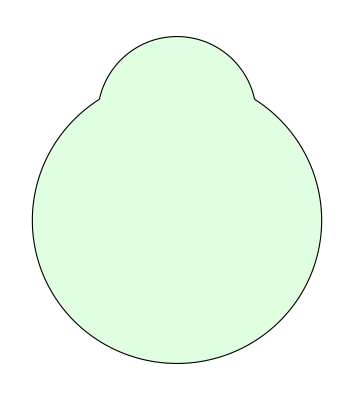

```mathematica
Graphics[PolyG[format]]
```

```mathematica
Vn=ReadList[path<>"view_new.dat",Real];
Tn=ReadList[path<>"triangles_new.dat",Table[{Real,Real,Real},3]];
Mn=ReadList[path<>"mask_new.dat",Number];

Colsn=If[#>0.99,Yellow, If[#>0,Red,Blue]]&/@Mn;
```

```mathematica
gn=Graphics3D[
{
{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},Vn},0.01]]},
{EdgeForm[],Transpose[{Colsn,Triangle/@Tn}]}
},
Ticks->Automatic,
Axes->True,
AxesLabel->{"x","y","z"},
ImageSize->600,PlotRangePadding->0]
```

-Graphics3D-

## Plotting results 2

```mathematica
Clear[ParseAsPolygons];
ParseAsPolygons[l_List]:=Module[{n,m,res},
m=l;
res={};
While[
Length[m]≠0,
n=First[m];
m=Rest[m];
AppendTo[res,Partition[Take[m,3*n],3]];
m=Drop[m,3*n];
];
res
];
```

```mathematica
V1[[1]]
```

0.939693

```mathematica
V1=ReadList[path<>"view_new.dat",Real];
T1=ReadList[path<>"triangles_new.dat",Table[{Real,Real,Real},3]];
M1=ReadList[path<>"mask_new.dat",Number];
H1=ParseAsPolygons[ReadList[path<>"horizon.dat",Number]];

Col1=If[#>0.99,Yellow, If[#>0,Red,Blue]]&/@M1;
```

```mathematica
gn=Graphics3D[
{
{Red,Arrowheads[0.3],Arrow[Tube[{{0,0,0},V1*0.5},0.01]]},
{EdgeForm[],Transpose[{Col1,Triangle/@T1}]},
{Red,Line[H1]}
},
Ticks->Automatic,
Axes->True,
AxesLabel->{"x","y","z"},
ImageSize->600,PlotRangePadding->0]
```

-Graphics3D-